```mathematica
a[ψ_, τ_, t_] :=Sin[ψ(1 -τ/t)]/Sin[ψ];
b[ψ_, τ_, t_] :=Sin[ψ τ/t]/Sin[ψ];
n[ψ_, τ_,t_]:=(a[ψ, τ, t]+ b[ψ, τ,t]-1)/(a[ψ, t/2,t]+b[ψ, t/2,t] - 1);
γ[ψ_, τ_, t_, λ_]:=Sqrt[1- λ^2 (n[ψ, τ, t])^2];
γa[ψ_, τ_, t_,  λ_]:=γ[ψ, τ, t, λ] a[ψ, τ, t];
γb[ψ_, τ_, t_,  λ_]:=γ[ψ, τ, t, λ] b[ψ, τ, t];
```

```mathematica
Integrate[a[ψ, τ, t], {τ, 0,t}]
Integrate[b[ψ, τ, t], {τ, 0,t}]
Integrate[n[ψ, τ, t], {τ, 0,t}]
```

(t Tan[ψ/2])/ψ

(t Tan[ψ/2])/ψ

(t (ψ+4 Cot[ψ/4]-ψ Cot[ψ/4]^2))/(2 ψ)

```mathematica
Integrate[a[Subscript[ψ, 1], τ, t]a[Subscript[ψ, 2], τ, t],{τ,0, t}]
Integrate[b[Subscript[ψ, 1], τ, t]b[Subscript[ψ, 2], τ, t],{τ,0, t}]
Integrate[n[Subscript[ψ, 1], τ, t]n[Subscript[ψ, 2], τ, t],{τ,0, t}]
```

(-t Cot[ψ_1] ψ_1+t Cot[ψ_2] ψ_2)/(ψ_1^2-ψ_2^2)

(-t Cot[ψ_1] ψ_1+t Cot[ψ_2] ψ_2)/(ψ_1^2-ψ_2^2)

(t (-ψ_1 ψ_2^3+2 ψ_2^3 Tan[ψ_1/2]+ψ_1^3 (ψ_2-2 Tan[ψ_2/2])))/((-1+Sec[ψ_1/2]) (-1+Sec[ψ_2/2]) ψ_1 ψ_2 (ψ_1^2-ψ_2^2))

```mathematica
Integrate[a[Subscript[ψ, 1], τ, t]b[Subscript[ψ, 2], τ, t],{τ,0, t}]
Integrate[a[Subscript[ψ, 1], τ, t]n[Subscript[ψ, 2], τ, t],{τ,0, t}]
Integrate[b[Subscript[ψ, 1], τ, t]n[Subscript[ψ, 2], τ, t],{τ,0, t}]
```

(t (Csc[ψ_1] ψ_1-Csc[ψ_2] ψ_2))/(ψ_1^2-ψ_2^2)

(t ψ_2 (-ψ_2 Tan[ψ_1/2]+ψ_1 Tan[ψ_2/2]))/((-1+Sec[ψ_2/2]) ψ_1 (-ψ_1^2+ψ_2^2))

(t ψ_2 (-ψ_2 Tan[ψ_1/2]+ψ_1 Tan[ψ_2/2]))/((-1+Sec[ψ_2/2]) ψ_1 (-ψ_1^2+ψ_2^2))

(t ψ_2 (-ψ_2 Tan[ψ_1/2]+ψ_1 Tan[ψ_2/2]))/((-1+Sec[ψ_2/2]) ψ_1 (-ψ_1^2+ψ_2^2))

«1 more identical outputs»

```mathematica
Integrate[(1- λ^2 (n[ψ, τ, t])^2 )(a[ψ, τ, t])^2,{τ, 0, 1}]
Integrate[(1- λ^2 (n[ψ, τ, t])^2) (b[ψ, τ, t])^2,{τ, 0, 1}]
Integrate[(1- λ^2 (n[ψ, τ, t])^2) (a[ψ, τ, t]b[ψ, τ, t]),{τ, 0, 1}]
```

Csc[ψ]^2 ((Csc[ψ/4]^4 (-6 t Sin[ψ]+18 t λ^2 Sin[ψ]+24 t Sin[(3 ψ)/2]-36 t Sin[2 ψ]-8 t λ^2 Sin[2 ψ]+24 t Sin[(5 ψ)/2]-6 t Sin[3 ψ]+t λ^2 Sin[3 ψ]))/(384 ψ)-1/(384 ψ)Csc[ψ/4]^4 (-72 ψ+48 λ^2 ψ+96 ψ Cos[ψ/2]+12 (-2+λ^2) ψ Cos[ψ]+3 t λ^2 Sin[(3-4/t) ψ]-8 t λ^2 Sin[(2-3/t) ψ]+24 t Sin[(3/2-2/t) ψ]+24 t Sin[(5/2-2/t) ψ]-6 t Sin[(3-2/t) ψ]+6 t λ^2 Sin[(3-2/t) ψ]-24 t λ^2 Sin[(2-1/t) ψ]-48 t λ^2 Sin[ψ/t]-36 t Sin[(2 (-1+t) ψ)/t]+24 t λ^2 Sin[(2 (-1+t) ψ)/t]-8 t λ^2 Sin[(3 (-1+t) ψ)/t]-6 t Sin[ψ-(2 ψ)/t]-6 t λ^2 Sin[ψ-(2 ψ)/t]+24 t λ^2 Sin[ψ-ψ/t]))

1/(384 ψ)Csc[ψ/4]^4 Csc[ψ]^2 (72 ψ-48 λ^2 ψ-96 ψ Cos[ψ/2]-12 (-2+λ^2) ψ Cos[ψ]+55 t λ^2 Sin[ψ]-24 t λ^2 Sin[(1+1/t) ψ]+24 t λ^2 Sin[ψ/t]-36 t Sin[(2 ψ)/t]+24 t λ^2 Sin[(2 ψ)/t]-8 t λ^2 Sin[(3 ψ)/t]-24 t Sin[((-4+t) ψ)/(2 t)]-3 t λ^2 Sin[((-4+t) ψ)/t]+8 t λ^2 Sin[((-3+t) ψ)/t]+6 t Sin[((-2+t) ψ)/t]+6 t λ^2 Sin[((-2+t) ψ)/t]-48 t λ^2 Sin[((-1+t) ψ)/t]-6 t Sin[((2+t) ψ)/t]+6 t λ^2 Sin[((2+t) ψ)/t]+24 t Sin[((4+t) ψ)/(2 t)])

1/(1536 ψ (Cos[ψ/4]+Cos[(3 ψ)/4])^2)Csc[ψ/4]^6 (-12 ψ+48 ψ Cos[ψ/2]+24 (-3+2 λ^2) ψ Cos[ψ]+48 ψ Cos[(3 ψ)/2]-12 ψ Cos[2 ψ]+12 λ^2 ψ Cos[2 ψ]-24 t Sin[ψ/2]+36 t Sin[ψ]+8 t λ^2 Sin[ψ]-24 t Sin[(3 ψ)/2]+6 t Sin[2 ψ]-19 t λ^2 Sin[2 ψ]-8 t λ^2 Sin[(2-3/t) ψ]+24 t Sin[(3/2-2/t) ψ]+24 t λ^2 Sin[(2-1/t) ψ]-24 t λ^2 Sin[(1+1/t) ψ]+8 t λ^2 Sin[(-1+3/t) ψ]+6 t Sin[(2 ψ)/t]+24 t Sin[((-4+t) ψ)/(2 t)]-36 t Sin[((-2+t) ψ)/t]+24 t λ^2 Sin[((-2+t) ψ)/t]+3 t λ^2 Sin[(2 (-2+t) ψ)/t]-6 t Sin[(2 (-1+t) ψ)/t])

```mathematica
Integrate[γa[Subscript[ψ, 1], τ, t, Subscript[λ, 1]]γa[Subscript[ψ, 2], τ, t, Subscript[λ, 2]],{τ,0, t}]
```

∫_0^t Csc[ψ_1] Csc[ψ_2] Sin[(1-τ/t) ψ_1] Sin[(1-τ/t) ψ_2] √(1-((-1+Csc[ψ_1] Sin[(τ ψ_1)/t]+Csc[ψ_1] Sin[(1-τ/t) ψ_1])^2 λ_1^2)/(-1+2 Csc[ψ_1] Sin[ψ_1/2])^2) √(1-((-1+Csc[ψ_2] Sin[(τ ψ_2)/t]+Csc[ψ_2] Sin[(1-τ/t) ψ_2])^2 λ_2^2)/(-1+2 Csc[ψ_2] Sin[ψ_2/2])^2)ⅆτ

```mathematica
aavg = Integrate[a[ψ, τ, t], {τ,0, t}]/t
bavg = Integrate[b[ψ, τ, t], {τ,0, t}]/t
navg = Integrate[n[ψ, τ, t], {τ,0, t}]/t
```

Tan[ψ/2]/ψ

Tan[ψ/2]/ψ

(ψ+4 Cot[ψ/4]-ψ Cot[ψ/4]^2)/(2 ψ)

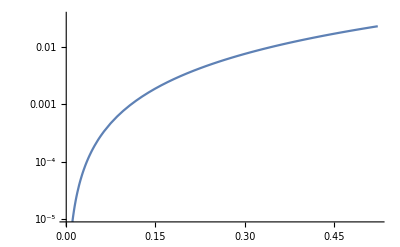

```mathematica
LogPlot[Abs[((2(Tan[ψ/2])^2)/ψ^2(1 + Cos[ψ])-1)], {ψ, 0, π/6}]
```